## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 3

### Reproduce frequency drift feature

#### The position of the electron beam is given by the classical velocity, where we take the velocity to be 0.3c

```mathematica
r =(Rs+ 0.3 c tE)/Rs;
```

#### The frequency of the emitted radiation as a function of radius is (in MHz)

```mathematica
fE = 8980 √ne/10^6;
```

#### In the last problem, we found the number density as

```mathematica
ne = α/r^2+β/r^4+γ/r^6/.{α-> 3.3 10^5,β-> 4.1 10^6,γ-> 8 10^7};
```

#### The time the signal arrives at earth is given by

```mathematica
t ==  tE + (RE -Rs r)/c;
```

#### Solve the equation for tE

```mathematica
tE = Part[Solve[t ==  tE + (RE -Rs r)/c ,tE],1,1,2]//FullSimplify
```

(-1.42857 RE+1.42857 Rs+1.42857 c t)/c

#### The pertinent values for this equation are

```mathematica
fEv = {c-> 3 10^10,RE ->  1.5 10^13,Rs-> 6.96 10^10};
```

#### The start time is offset by the light travel time between the earth and the sn

```mathematica
tStart = (RE - Rs)/c /. fEv
```

497.68

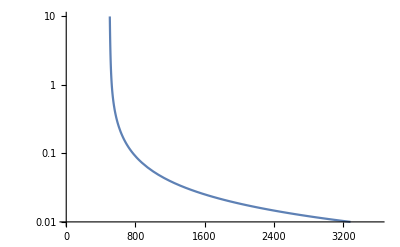

```mathematica
p0 =LogPlot[{fE /. {c-> 3 10^10,RE ->  1.5 10^13,Rs-> 6.96 10^10}},{t,tStart,3600},PlotRange->{{0, 3600},{0.01,10}}]
```

### Reproduce type-III radio burst dynamic spectrum

#### The time-evolution of the peak frequency of type-III radio bursts follows the empirical power law

```mathematica
f = a t^b ;
fv ={a-> 150,b-> -0.6 };
```

#### The FWHM of these bursts is given by the empirical law

```mathematica
Δf = C1 ν;
Δfv = {C1-> 0.57};
```

#### and the empirical frequency-dependent decay is

```mathematica
τD = 10^γ(10^6 ν)^-δ/. ν-> 0.1;
τDv = {γ-> 7.71,δ-> 0.95};
```

#### Plot the dynamic frequency using the curve developed in the first part of the question.

```mathematica
S1=Piecewise[{{Exp[-(4 Log[2](ν - fE)^2)/Δf^2] Exp[-(t-tStart)/τD]/.ν-> 10^ν,t >tStart},{0,t<tStart}}];
p1=DensityPlot[S1/. fv/.Δfv /. τDv /. fEv ,{t,0,3600},{ν,-2,2},ColorFunction->"Rainbow",PlotRange->Full,PlotPoints->100,MaxRecursion->5]
```

-Graphics-

#### Plot the dynamic spectrum using the empirical power law

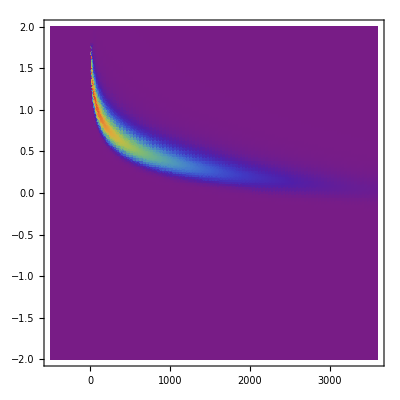

```mathematica
S2=Piecewise[{{Exp[-(4 Log[2](ν - f)^2)/Δf^2] Exp[-(t)/τD]/.ν-> 10^ν,t >0},{0,t<0}}];
p1=DensityPlot[S2/. fv/.Δfv /. τDv /. fEv ,{t,-tStart,3600},{ν,-2,2},ColorFunction->"Rainbow",PlotRange->Full,PlotPoints->100,MaxRecursion->5]
```

#### Comparing to Figure 1 in the Problem Statement, the empirical law and the law derived from the plasma frequency in the heliosphere did not quite match. General shape seems to be correct.